```mathematica
Clear[u]
DSolve[{D[u[x,t], t]+a*D[u[x,t],x]==0}, u[x,t], {x,t}][[1,1]]
```

u[x,t]→C[1][t-x/a]

```mathematica
DSolve[{D[u1[x,t], t]+a[x]*D[u1[x,t],x]==0}, u1[x,t], {x,t}][[1,1]]
```

u1[x,t]→C[1][t-1/a[K[1]]K[1]1x]

```mathematica
DSolve[{D[u3[x,t], t]+(x-t)*D[u3[x,t],x]==0}, u3[x,t], {x,t}][[1,1]]
```

DSolve::ifun: Inverse functions are being used by DSolve, so some solutions may not be found.

u3[x,t]→C[1][ⅇ^-t (-1-t+x)]

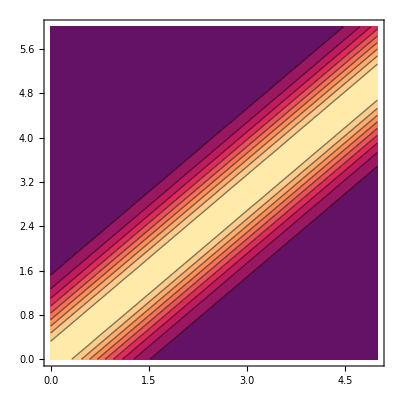

-Graphics3D-

```mathematica
a=1;
phi1[z_]:=Exp[-z^2]
phi[x_,t_]:=phi1[x-a*t];
ContourPlot[phi[x, t], {x,0,5}, {t,0,6}]
Plot3D[phi[x,t],{x,0,5},{t,0,6}]
```

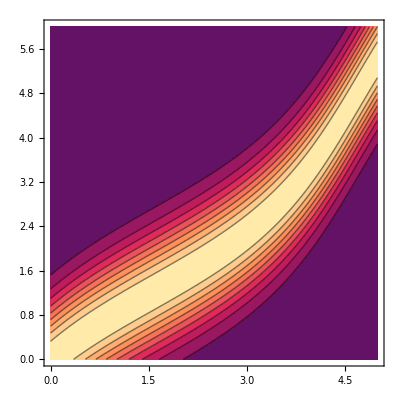

-Graphics3D-

```mathematica
ClearAll["Global`*"]
a[x_]:=1+0.5*Sin[x];
fsol=NDSolve[{f'[x]==1/a[x],f[0]==0},f,{x,0,5}][[1]];
phi0[z_]:=Exp[-z^2];
u[x_?NumericQ,t_?NumericQ]:=phi0[t-(f[x]/. fsol)];
ContourPlot[u[x,t],{x,0,5},{t,0,6},PlotPoints->50]
Plot3D[u[x,t],{x,0,5},{t,0,6}]
```

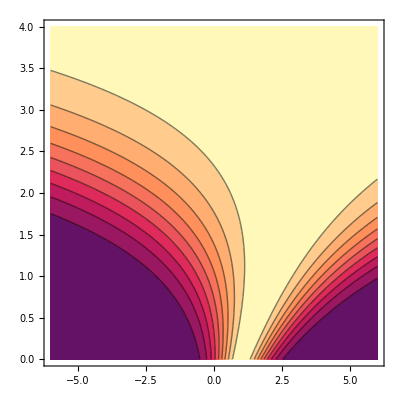

-Graphics3D-

```mathematica
ClearAll["Global`*"]
phi0[z_]:=Exp[-z^2];
u[x_?NumericQ,t_?NumericQ]:=phi0[Exp[-t]*(x-1-t)];
ContourPlot[u[x,t],{x,-6,6},{t,0,4},PlotPoints->50]
Plot3D[u[x,t],{x,-6,6},{t,0,4}, PlotRange->All]
```

```mathematica
analitprobfunc[x_]:=UnitStep[x];
phi[x_,t_]:=analitprobfunc[x-t];

Manipulate[Plot[phi[x,t],{x,-5,15},PlotRange->{-0.1,1.1},AxesLabel->{"x","φ(x,t)"}],{t,0,10,0.1}]
```

```mathematica
a[x_]:=1+0.5 Sin[x];
analitprobfuncax[x_]:=UnitStep[x];
fsol=NDSolve[{f'[x]==1/a[x],f[0]==0},f,{x,-10,10}][[1]];
uAnalytic[x_?NumericQ,t_?NumericQ]:=analitprobfuncax[-t+(f[x]/. fsol)];
Manipulate[Plot[uAnalytic[x,t],{x,-10,10},PlotRange->{-0.1,1.1},AxesLabel->{"x","φ(x,t)"}],{t,0,10,0.1}]
```

```mathematica
a[x_]:=1+0.5 Sin[x];
analitprobfuncxt[x_]:=UnitStep[x];
uAnalyticxt[x_?NumericQ,t_?NumericQ]:=analitprobfuncxt[Exp[-t]*(x-1-t)];
Manipulate[Plot[uAnalyticxt[x,t],{x,-10,10},PlotRange->{-0.1,1.1},AxesLabel->{"x","φ(x,t)"}],{t,0,10,0.1}]
```

```mathematica
ClearAll["Global`*"]
a=1;
h=0.25;
tau=0.05;
lambda=a*tau/h;
xmax=20;
nstep=500;
(*phi[x_]:=Exp[-(x+1)^2];*)
(*probfunc[x_]:=1/(1+Exp[-10*x]);*)

probfunc[x_]:=UnitStep[x]
uAnalytic[x_,t_]:=probfunc[x-a t];xgrid=Range[-xmax,xmax,h];
```

```mathematica
(*---Явная схема (против потока)---*)
uLeft[t_]:=probfunc[-xmax-a t];
uRight[t_]:=probfunc[xmax-a t];

uJavnmeth=ConstantArray[0,{1+nstep,Length[xgrid]}];
uJavnmeth[[1]]=probfunc/@xgrid;
Do[Do[uJavnmeth[[n+1,i]]=uJavnmeth[[n,i]]-lambda*(uJavnmeth[[n,i]]-uJavnmeth[[n,i-1]]);,{i,2,Length[xgrid]-1}];
uJavnmeth[[n+1,1]]=uLeft[n*tau];
uJavnmeth[[n+1,-1]]=uRight[n*tau];
,{n,1,nstep}]
```

```mathematica
(*---Явная схема (Лакс-Фридрихс)---*)
uLeft[t_]:=probfunc[-xmax-a t];
uRight[t_]:=probfunc[xmax-a t];

uJavnLaxFrid=ConstantArray[0,{1+nstep,Length[xgrid]}];
uJavnLaxFrid[[1]]=probfunc/@xgrid;
Do[
Do[
uJavnLaxFrid[[n+1,i]]=1/2*(uJavnLaxFrid[[n,i+1]]+uJavnLaxFrid[[n,i-1]])-lambda/2*(uJavnLaxFrid[[n,i+1]]-uJavnLaxFrid[[n,i-1]]);,{i,2,Length[xgrid]-1}];
uJavnLaxFrid[[n+1,1]]=uLeft[n*tau];
uJavnLaxFrid[[n+1,-1]]=uRight[n*tau];
,{n,1,nstep}]
```

```mathematica
(*---Явная схема (Лакс-Вендрофф)---*)
uLeft[t_]:=probfunc[-xmax-a t];
uRight[t_]:=probfunc[xmax-a t];

uJavnLaxVander=ConstantArray[0,{1+nstep,Length[xgrid]}];
uJavnLaxVander[[1]]=probfunc/@xgrid;
Do[
Do[
uJavnLaxVander[[n+1,i]]=uJavnLaxVander[[n,i]]-lambda/2*(uJavnLaxVander[[n,i+1]]-uJavnLaxVander[[n,i-1]])+lambda^2/2*(uJavnLaxVander[[n,i+1]]-2*uJavnLaxVander[[n,i]]+uJavnLaxVander[[n,i-1]]);,{i,2,Length[xgrid]-1}];
uJavnLaxVander[[n+1,1]]=uLeft[n*tau];
uJavnLaxVander[[n+1,-1]]=uRight[n*tau];
,{n,1,nstep}]
```

```mathematica
(*---Явная схема (TVD)---*)
uLeft[t_]:=probfunc[-xmax-a t];
uRight[t_]:=probfunc[xmax-a t];

uJavnTVD=ConstantArray[0,{1+nstep,Length[xgrid]}];
uJavnTVD[[1]]=probfunc/@xgrid;
Do[
Do[delm=uJavnTVD[[n,i]]-uJavnTVD[[n,i-1]];
delp=uJavnTVD[[n,i+1]]-uJavnTVD[[n,i]];
r=If[delp==0,0,delm/delp];
phi=Max[0,Min[1,r]];
delmleft=uJavnTVD[[n,i-1]]-uJavnTVD[[n,i-2]];
delpleft=delm;
rleft=If[delpleft==0,0,delmleft/delpleft];
phileft=Max[0,Min[1,rleft]];
correction=phi*delp-phileft*delm;
uJavnTVD[[n+1,i]]=uJavnTVD[[n,i]]-lambda*delm-(lambda*(1-lambda)/2)*correction;,{i,3,Length[xgrid]-1}];
uJavnTVD[[n+1,1]]=uLeft[n*tau];
uJavnTVD[[n+1,2]]=uJavnTVD[[n+1,3]];
uJavnTVD[[n+1,-1]]=uRight[n*tau];
uJavnTVD[[n+1, -2]]=uJavnTVD[[n+1,-3]]
,{n,1,nstep}]
```

```mathematica
Manipulate[ListLinePlot[{Transpose[{xgrid,uJavnmeth[[n]]}],
Transpose[{xgrid,uJavnLaxFrid[[n]]}],Transpose[{xgrid,uJavnLaxVander[[n]]}],Transpose[{xgrid,uJavnTVD[[n]]}],Transpose[{xgrid,uAnalytic[#,(n-1) tau]&/@xgrid}]},PlotRange->All,PlotStyle->{Red,Blue, Orange,Green, White},PlotLegends->{"Явная схема (против потока)","Явная схема (Лакса-Фридриха)","Явная схема (Лакса-Вендроффа)","Явная схема (TVD)","Аналитическое решение"},GridLines->Automatic],{n,1,nstep,1}]
```

```mathematica
ClearAll["Global`*"]
h=0.25;
tau=0.05;
xmax=20;
nstep=500;
(*phi[x_]:=Exp[-(x+1)^2];*)
(*probfunc[x_]:=1/(1+Exp[-10*x]);*)
a[x_]:=1+0.5 Sin[x];
probfunc[x_]:=UnitStep[x]
fsol=NDSolve[{f'[x]==1/a[x],f[0]==0},f,{x,-xmax,xmax}][[1]];
uAnalytic[x_?NumericQ,t_?NumericQ]:=probfunc[-t+(f[x]/. fsol)];xgrid=Range[-xmax,xmax,h];
```

```mathematica
(*---Явная схема (против потока)---*)
uLeft[t_]:=uAnalytic[-xmax,t];
uRight[t_]:=uAnalytic[xmax,t];

uJavnmeth=ConstantArray[0,{1+nstep,Length[xgrid]}];
uJavnmeth[[1]]=probfunc/@xgrid;
Do[
Do[
ai=a[xgrid[[i]]];
If[ai>0,
uJavnmeth[[n+1,i]]=uJavnmeth[[n,i]]-(ai*tau/h) (uJavnmeth[[n,i]]-uJavnmeth[[n,i-1]]),uJavnmeth[[n+1,i]]=uJavnmeth[[n,i]]-(ai*tau/h) (uJavnmeth[[n,i+1]]-uJavnmeth[[n,i]])];
,{i,2,Length[xgrid]-1}];
uJavnmeth[[n+1,1]]=uLeft[n*tau];
uJavnmeth[[n+1,-1]]=uRight[n*tau];
,{n,1,nstep}]
```

```mathematica
(*---Явная схема (Лакс-Фридрихс)---*)
uLeft[t_]:=uAnalytic[-xmax,t];
uRight[t_]:=uAnalytic[xmax,t];

uJavnLaxFrid=ConstantArray[0,{1+nstep,Length[xgrid]}];
uJavnLaxFrid[[1]]=probfunc/@xgrid;
Do[
Do[
ai=a[xgrid[[i]]];
lambdaax=ai*tau/h;
uJavnLaxFrid[[n+1,i]]=1/2*(uJavnLaxFrid[[n,i+1]]+uJavnLaxFrid[[n,i-1]])-lambdaax/2*(uJavnLaxFrid[[n,i+1]]-uJavnLaxFrid[[n,i-1]]);,{i,2,Length[xgrid]-1}];
uJavnLaxFrid[[n+1,1]]=uLeft[n*tau];
uJavnLaxFrid[[n+1,-1]]=uRight[n*tau];
,{n,1,nstep}]
```

```mathematica
(*---Явная схема (Лакс-Вендрофф)---*)
uLeft[t_]:=uAnalytic[-xmax,t];
uRight[t_]:=uAnalytic[xmax,t];

uJavnLaxVander=ConstantArray[0,{1+nstep,Length[xgrid]}];
uJavnLaxVander[[1]]=probfunc/@xgrid;
Do[
Do[
ai=a[xgrid[[i]]];
lambdaax=ai*tau/h;
uJavnLaxVander[[n+1,i]]=uJavnLaxVander[[n,i]]-lambdaax/2*(uJavnLaxVander[[n,i+1]]-uJavnLaxVander[[n,i-1]])+lambdaax^2/2*(uJavnLaxVander[[n,i+1]]-2*uJavnLaxVander[[n,i]]+uJavnLaxVander[[n,i-1]]);,{i,2,Length[xgrid]-1}];
uJavnLaxVander[[n+1,1]]=uLeft[n*tau];
uJavnLaxVander[[n+1,-1]]=uRight[n*tau];
,{n,1,nstep}]
```

```mathematica
(*---Явная схема (TVD)---*)
uLeft[t_]:=uAnalytic[-xmax,t];
uRight[t_]:=uAnalytic[xmax,t];

uJavnTVD=ConstantArray[0,{1+nstep,Length[xgrid]}];
uJavnTVD[[1]]=probfunc/@xgrid;
Do[
Do[
ai=a[xgrid[[i]]];
lambdaax=ai*tau/h;
delm=uJavnTVD[[n,i]]-uJavnTVD[[n,i-1]];
delp=uJavnTVD[[n,i+1]]-uJavnTVD[[n,i]];
r=If[delp==0,0,delm/delp];
phi=Max[0,Min[1,r]];
delmleft=uJavnTVD[[n,i-1]]-uJavnTVD[[n,i-2]];
delpleft=delm;
rleft=If[delpleft==0,0,delmleft/delpleft];
phileft=Max[0,Min[1,rleft]];
correction=phi*delp-phileft*delm;
uJavnTVD[[n+1,i]]=uJavnTVD[[n,i]]-lambdaax*delm-(lambdaax*(1-lambdaax)/2)*correction;,{i,3,Length[xgrid]-1}];
uJavnTVD[[n+1,1]]=uLeft[n*tau];
uJavnTVD[[n+1,2]]=uJavnTVD[[n+1,3]];
uJavnTVD[[n+1,-1]]=uRight[n*tau];
uJavnTVD[[n+1, -2]]=uJavnTVD[[n+1,-3]]
,{n,1,nstep}]
```

```mathematica
Manipulate[ListLinePlot[{
Transpose[{xgrid,uJavnmeth[[n]]}],
Transpose[{xgrid,uJavnLaxFrid[[n]]}],
Transpose[{xgrid,uJavnLaxVander[[n]]}],
Transpose[{xgrid,uJavnTVD[[n]]}],
Transpose[{xgrid,uAnalytic[#,(n-1) tau]&/@xgrid}]},PlotRange->All,PlotStyle->{Red,Blue, Orange,Green, White},PlotLegends->{"Явная схема (против потока)","Явная схема (Лакса-Фридриха)","Явная схема (Лакса-Вендроффа)","Явная схема (TVD)","Аналитическое решение"},GridLines->Automatic],{n,1,nstep,1}]
```

```mathematica
ClearAll["Global`*"]
h=0.25;
tau=0.05;
xmax=20;
nstep=500;
(*phi[x_]:=Exp[-(x+1)^2];*)
(*probfunc[x_]:=1/(1+Exp[-10*x]);*)
a[x_]:=1+0.5 Sin[x];
probfunc[x_]:=UnitStep[x]
uAnalytic[x_?NumericQ,t_?NumericQ]:=probfunc[Exp[-t]*(x-1-t)+Exp[-t]];xgrid=Range[-xmax,xmax,h];
```

```mathematica
(*---Явная схема (против потока)---*)
uLeft[t_]:=uAnalytic[-xmax,t];
uRight[t_]:=uAnalytic[xmax,t];

uJavnmeth=ConstantArray[0,{1+nstep,Length[xgrid]}];
uJavnmeth[[1]]=probfunc/@xgrid;
Do[
tCurr=(n-1)*tau;
Do[
ai=xgrid[[i]]-tCurr;
If[ai>0,
uJavnmeth[[n+1,i]]=uJavnmeth[[n,i]]-(Abs[ai] tau/h) (uJavnmeth[[n,i]]-uJavnmeth[[n,i-1]]),uJavnmeth[[n+1,i]]=uJavnmeth[[n,i]]-(Abs[ai] tau/h) (uJavnmeth[[n,i+1]]-uJavnmeth[[n,i]])]
,{i,2,Length[xgrid]-1}];
uJavnmeth[[n+1,1]]=uLeft[tCurr];
uJavnmeth[[n+1,-1]]=uRight[tCurr];
,{n,1,nstep}]
```

```mathematica
(*---Явная схема консервативная (против потока)---*)
uLeft[t_]:=uAnalytic[-xmax,t];
uRight[t_]:=uAnalytic[xmax,t];
uJavnmethCons=ConstantArray[0,{1+nstep,Length[xgrid]}];
uJavnmethCons[[1]]=probfunc/@xgrid;

Do[tCurr=(n-1)*tau;
Do[aiLeft=(xgrid[[i-1]]-tCurr+xgrid[[i]]-tCurr)/2;(*a на левой границе*)aiRight=(xgrid[[i]]-tCurr+xgrid[[i+1]]-tCurr)/2;(*a на правой границе*)FLeft=If[aiLeft>0,aiLeft*uJavnmethCons[[n,i-1]],aiLeft*uJavnmethCons[[n,i]]];
FRight=If[aiRight>0,aiRight*uJavnmethCons[[n,i]],aiRight*uJavnmethCons[[n,i+1]]];
uJavnmethCons[[n+1,i]]=uJavnmethCons[[n,i]]-(tau/h)*(FRight-FLeft);,{i,2,Length[xgrid]-1}];
uJavnmethCons[[n+1,1]]=uLeft[tCurr];
uJavnmethCons[[n+1,-1]]=uRight[tCurr];,{n,1,nstep}]
```

```mathematica
(*---Явная схема (Лакс-Фридрихс)---*)
uLeft[t_]:=uAnalytic[-xmax,t];
uRight[t_]:=uAnalytic[xmax,t];

uJavnLaxFrid=ConstantArray[0,{1+nstep,Length[xgrid]}];
uJavnLaxFrid[[1]]=probfunc/@xgrid;
Do[
tCurr=(n-1)*tau;
Do[
ai=xgrid[[i]]-tCurr;
lambdaai=Abs[ai] tau/h;
lambdaax=ai*tau/h;
uJavnLaxFrid[[n+1,i]]=1/2*(uJavnLaxFrid[[n,i+1]]+uJavnLaxFrid[[n,i-1]])-lambdaai/2*(uJavnLaxFrid[[n,i+1]]-uJavnLaxFrid[[n,i-1]]);,{i,2,Length[xgrid]-1}];
uJavnLaxFrid[[n+1,1]]=uLeft[n*tau];
uJavnLaxFrid[[n+1,-1]]=uRight[n*tau];
,{n,1,nstep}]
```

```mathematica
(*---Явная схема (Лакс-Вендрофф)---*)
uLeft[t_]:=uAnalytic[-xmax,t];
uRight[t_]:=uAnalytic[xmax,t];

uJavnLaxVander=ConstantArray[0,{1+nstep,Length[xgrid]}];
uJavnLaxVander[[1]]=probfunc/@xgrid;
Do[
tCurr=(n-1)*tau;
Do[
ai=xgrid[[i]]-tCurr;
lambdaax=ai*tau/h;
uJavnLaxVander[[n+1,i]]=uJavnLaxVander[[n,i]]-lambdaax/2*(uJavnLaxVander[[n,i+1]]-uJavnLaxVander[[n,i-1]])+lambdaax^2/2*(uJavnLaxVander[[n,i+1]]-2*uJavnLaxVander[[n,i]]+uJavnLaxVander[[n,i-1]]);,{i,2,Length[xgrid]-1}];
uJavnLaxVander[[n+1,1]]=uLeft[n*tau];
uJavnLaxVander[[n+1,-1]]=uRight[n*tau];
,{n,1,nstep}]
```

```mathematica
(*---Явная схема (TVD)---*)
uLeft[t_]:=uAnalytic[-xmax,t];
uRight[t_]:=uAnalytic[xmax,t];

uJavnTVD=ConstantArray[0,{1+nstep,Length[xgrid]}];
uJavnTVD[[1]]=probfunc/@xgrid;
Do[
tCurr=(n-1)*tau;
Do[
ai=xgrid[[i]]-tCurr;
lambdaax=ai*tau/h;
delm=uJavnTVD[[n,i]]-uJavnTVD[[n,i-1]];
delp=uJavnTVD[[n,i+1]]-uJavnTVD[[n,i]];
r=If[delp==0,0,delm/delp];
phi=Max[0,Min[1,r]];
delmleft=uJavnTVD[[n,i-1]]-uJavnTVD[[n,i-2]];
delpleft=delm;
rleft=If[delpleft==0,0,delmleft/delpleft];
phileft=Max[0,Min[1,rleft]];
correction=phi*delp-phileft*delm;
uJavnTVD[[n+1,i]]=uJavnTVD[[n,i]]-lambdaax*delm-(lambdaax*(1-lambdaax)/2)*correction;,{i,3,Length[xgrid]-1}];
uJavnTVD[[n+1,1]]=uLeft[n*tau];
uJavnTVD[[n+1,2]]=uJavnTVD[[n+1,3]];
uJavnTVD[[n+1,-1]]=uRight[n*tau];
uJavnTVD[[n+1, -2]]=uJavnTVD[[n+1,-3]]
,{n,1,nstep}]
```

```mathematica
Manipulate[ListLinePlot[{
Transpose[{xgrid,uJavnmeth[[n]]}],
(*Transpose[{xgrid,uJavnmethCons[[n]]}],*)
Transpose[{xgrid,uJavnLaxFrid[[n]]}],
Transpose[{xgrid,uJavnLaxVander[[n]]}],
Transpose[{xgrid,uJavnTVD[[n]]}],
Transpose[{xgrid,uAnalytic[#,(n-1) tau]&/@xgrid}]},PlotRange->All,PlotStyle->{Red,Blue, Orange,Green, White},PlotLegends->{"Явная схема (против потока)","Явная схема (Лакса-Фридриха)","Явная схема (Лакса-Вендроффа)","Явная схема (TVD)","Аналитическое решение"},GridLines->Automatic],{n,1,nstep,1}]
```

```mathematica
ClearAll["Global`*"]
(*Параметры*)
h=0.25;tau=0.05;xmax=20;nstep=500;
xgrid=Range[-xmax,xmax,h];

(*Исходная функция и аналитическое решение*)
probfunc[x_]:=UnitStep[x];
uAnalytic[x_?NumericQ,t_?NumericQ]:=probfunc[Exp[-t]*(x-1-t)+Exp[-t]];

(*Массив для решения*)
Nx=Length[xgrid];
uImplicitXT=ConstantArray[0,{1+nstep,Nx}];
uImplicitXT[[1]]=probfunc/@xgrid;

(*Функция для вычисления потоков по upwind*)
ClearAll[ComputeFlux]
ComputeFlux[u_?VectorQ,a_?NumericQ,i_]:=If[a>=0,a u[[i]],a u[[i+1]]];

(*Основной цикл по времени*)
Do[tCurr=n tau;
uNew=uImplicitXT[[n]];
(*Итерация для неявного шага (Picard)*)Do[uOld=uNew;
(*Ghost cells для границ*)uGhostLeft=2 uAnalytic[xgrid[[1]],tCurr]-uOld[[1]];
uGhostRight=2 uAnalytic[xgrid[[Nx]],tCurr]-uOld[[Nx]];
Do[aiLeft=xgrid[[i-1]]-tCurr;
aiRight=xgrid[[i]]-tCurr;
(*Используем ghost cells на концах*)uLeftCell=If[i==2,uGhostLeft,uOld[[i-1]]];
uRightCell=If[i==Nx-1,uGhostRight,uOld[[i+1]]];
FLeft=ComputeFlux[uOld/. {i->uLeftCell},aiLeft,i-1];
FRight=ComputeFlux[uOld/. {i->uRightCell},aiRight,i];
uNew[[i]]=uImplicitXT[[n,i]]-(tau/h) (FRight-FLeft);,{i,2,Nx-1}];
(*Левая и правая границы*)uNew[[1]]=uAnalytic[xgrid[[1]],tCurr];
uNew[[Nx]]=uAnalytic[xgrid[[Nx]],tCurr];,{iter,1,3} (*3 итерации Picard*)];
uImplicitXT[[n+1]]=uNew;,{n,1,nstep}];

(*Визуализация*)
Manipulate[ListLinePlot[{Transpose[{xgrid,uImplicitXT[[n]]}],Transpose[{xgrid,uAnalytic[#,(n-1) tau]&/@xgrid}]},PlotRange->All,PlotStyle->{Red,Blue},PlotLegends->{"Неявная схема (Picard + ghost cells)","Аналитическое решение"}],{n,1,nstep,1}]
```

```mathematica
ClearAll["Global`*"];

(*Параметры*)
h=0.25;
tau=0.05;
xmax=20;
nstep=500;

(*Пробная функция:ступенька*)
probfunc[x_]:=UnitStep[x];

(*Пространственная сетка*)
xgrid=Range[-xmax,xmax,h];
Nx=Length[xgrid];

(*Переменная скорость*)
a[x_]:=1+0.5 Sin[x];

(*Граничные условия*)
uLeft[t_]:=probfunc[-xmax];  (*постоянная слева*)
uRight[t_]:=probfunc[xmax];  (*постоянная справа*)

(*---Аналитическое решение через характеристику---*)(*f[x]=интеграл 1/a(s) ds*)fsol=NDSolve[{f'[x]==1/a[x],f[0]==0},f,{x,-xmax,xmax}][[1]];

phi0[z_]:=probfunc[z];  (*начальное условие*)

uAnalytic[x_?NumericQ,t_?NumericQ]:=phi0[-t+(f[x]/. fsol)];

(*Массив для хранения решения*)
uJavnmeth=ConstantArray[0.,{1+nstep,Nx}];
uJavnmeth[[1]]=probfunc/@xgrid;  (*начальное условие*)

(*---Явная схема Upwind для переменной скорости---*)
Do[Do[ai=a[xgrid[[i]]];
lambdaCFL=Abs[ai] tau/h;
If[ai>0,(*поток слева направо*)uJavnmeth[[n+1,i]]=uJavnmeth[[n,i]]-lambdaCFL*(uJavnmeth[[n,i]]-uJavnmeth[[n,i-1]]),(*поток справа налево*)uJavnmeth[[n+1,i]]=uJavnmeth[[n,i]]-lambdaCFL*(uJavnmeth[[n,i+1]]-uJavnmeth[[n,i]])];,{i,2,Nx-1}];
(*Граничные условия*)uJavnmeth[[n+1,1]]=uLeft[n tau];
uJavnmeth[[n+1,Nx]]=uRight[n tau];,{n,1,nstep}];

(*---Анимация:численное и аналитическое решения---*)Manipulate[ListLinePlot[{Transpose[{xgrid,uJavnmeth[[n]]}],(*численное*)Transpose[{xgrid,Table[uAnalytic[xgrid[[i]],n*tau],{i,Nx}]}]  (*аналитическое*)},PlotStyle->{Red,Blue},PlotLegends->{"Upwind","Аналитическое решение"},GridLines->Automatic,PlotRange->{0,1.2}],{n,1,nstep,1}]
```

```mathematica
ClearAll["Global`*"]

(*---Параметры---*)
h=0.25;
tau=0.05;
xmax=20;
nstep=400;

(*---Начальная функция---*)
probfunc[x_]:=UnitStep[x];

(*---Сетка---*)
xgrid=Range[-xmax,xmax,h];
Nx=Length[xgrid];

(*---Переменная скорость---*)
a[x_]:=1+0.5 Sin[x];

(*---Границы---*)
uLeft[t_]:=probfunc[-xmax];
uRight[t_]:=probfunc[xmax];

(*---Аналитика (характеристики)---*)
fsol=NDSolve[{f'[x]==1/a[x],f[0]==0},f,{x,-xmax,xmax}][[1]];
uAnalytic[x_?NumericQ,t_?NumericQ]:=probfunc[-t+(f[x]/. fsol)];

(*---Массивы---*)
uUpwind=ConstantArray[0.,{nstep+1,Nx}];
uTVD=ConstantArray[0.,{nstep+1,Nx}];
uImplicit=ConstantArray[0.,{nstep+1,Nx}];

uUpwind[[1]]=probfunc/@xgrid;
uTVD[[1]]=probfunc/@xgrid;
uImplicit[[1]]=probfunc/@xgrid;

(*========================*)
(*1. Upwind (явная)*)
(*========================*)
Do[Do[ai=a[xgrid[[i]]];
cfl=Abs[ai] tau/h;
If[ai>0,uUpwind[[n+1,i]]=uUpwind[[n,i]]-cfl (uUpwind[[n,i]]-uUpwind[[n,i-1]]),uUpwind[[n+1,i]]=uUpwind[[n,i]]-cfl (uUpwind[[n,i+1]]-uUpwind[[n,i]])];,{i,2,Nx-1}];
uUpwind[[n+1,1]]=uLeft[n tau];
uUpwind[[n+1,Nx]]=uRight[n tau];,{n,1,nstep}];

(*========================*)
(*2. TVD (MUSCL+minmod)*)
(*========================*)
minmod[a_,b_]:=If[a b>0,Sign[a] Min[Abs[a],Abs[b]],0];

Do[Do[ai=a[xgrid[[i]]];
cfl=Abs[ai] tau/h;
duL=uTVD[[n,i]]-uTVD[[n,i-1]];
duR=uTVD[[n,i+1]]-uTVD[[n,i]];
slope=minmod[duL,duR];
If[ai>0,uTVD[[n+1,i]]=uTVD[[n,i]]-cfl (duL+0.5 (slope-minmod[uTVD[[n,i-1]]-uTVD[[n,i-2]],duL])),uTVD[[n+1,i]]=uTVD[[n,i]]-cfl (duR-0.5 (minmod[uTVD[[n,i+2]]-uTVD[[n,i+1]],duR]-slope))];,{i,3,Nx-2}];
uTVD[[n+1,1;;2]]=uLeft[n tau];
uTVD[[n+1,Nx-1;;Nx]]=uRight[n tau];,{n,1,nstep}];

(*========================*)
(*3. Неявная схема (a=const)*)
(*========================*)
a0=1;
lambda=a0 tau/h;

matA=SparseArray[{Band[{1,1}]->(1+lambda),Band[{2,1}]->-lambda},{Nx,Nx}];

Do[uImplicit[[n+1]]=LinearSolve[matA,uImplicit[[n]]];
uImplicit[[n+1,1]]=uLeft[n tau];
uImplicit[[n+1,Nx]]=uRight[n tau];,{n,1,nstep}];

(*========================*)
(*АНИМАЦИЯ*)
(*========================*)
Manipulate[ListLinePlot[{Transpose[{xgrid,uUpwind[[n]]}],Transpose[{xgrid,uTVD[[n]]}],Transpose[{xgrid,uImplicit[[n]]}],Transpose[{xgrid,Table[uAnalytic[xgrid[[i]],n tau],{i,Nx}]}]},PlotStyle->{Red,Orange,Green,Yellow},PlotLegends->{"Upwind","TVD","Implicit","Analytic"},PlotRange->{0,1.2},GridLines->Automatic],{n,1,nstep,1}]
```